```mathematica
dxf=Import["test6.dxf", "Graphics3D"]
```

-Graphics3D-

```mathematica
Show[dxf,Background->LightGray]
```

```mathematica
edg={1<->2,2<->6,3<->1,4<->1,5<->2,6<->12,7<->3,8<->4,9<->5,9<->11,10<->5, 10<->13, 11<->6, 13<->7, 13<->8, 14<->9, 15<->10, 15<->19, 16<->11, 17<->14, 17<-> 22, 18<->14, 19<->18, 20<->15,20<->24, 21<->16, 22<->16,
23<->17, 23<-> 28, 24<->23, 24<->26, 25<->20,26<->21, 27<->22, 28<->27};
```

```mathematica
edges={25<->20,20<->15,15<->10, 15<->19, 19<->18, 18<->14,14<->9,9<->11,10<->5,5<->2,9<->5,2<->6,10<->13,13<->7,7<->3,  3<->1,   13<->8,8<->4,4<->1,1<->2,6<->12,20<->24, 24<->23,23<-> 28,28<->27, 27<->22,22<->16,24<->26,26<->21, 21<->16,  16<->11,23<->17,  17<->14, 17<-> 22, 11<->6};
```

```mathematica
vd=Import["test6.dxf","VertexData"]
```

{{38.5,29.5,0},{44.5,40.8,0},{53.8,40.9,0},{57.6,35.2,0},{66.5,46.8,0},{83.3,46.3,0},{94.5,50.3,0},{111.9,57.4,0},{130.8,53.6,0},{100.4,46.9,0},{115.4,43.6,0},{126.6,38.8,0},{70.3,30.9,0},{82.8,35.3,0},{100.9,38.5,0},{109.9,36.5,0},{88.6,30.,0},{104.8,31.,0},{124.3,33.1,0},{50.,63.6,0},{55.8,53.9,0},{66.4,61.9,0},{84.2,59.6,0},{97.9,58.4,0},{113.1,66.6,0},{76.9,66.1,0},{96.6,63.7,0},{83.5,54.2,0}}

```mathematica
vl=Range[Length@vd]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28}

```mathematica
vcoords=MapIndexed[#2[[1]]->#&,vd]
```

{1→{38.5,29.5,0},2→{44.5,40.8,0},3→{53.8,40.9,0},4→{57.6,35.2,0},5→{66.5,46.8,0},6→{83.3,46.3,0},7→{94.5,50.3,0},8→{111.9,57.4,0},9→{130.8,53.6,0},10→{100.4,46.9,0},11→{115.4,43.6,0},12→{126.6,38.8,0},13→{70.3,30.9,0},14→{82.8,35.3,0},15→{100.9,38.5,0},16→{109.9,36.5,0},17→{88.6,30.,0},18→{104.8,31.,0},19→{124.3,33.1,0},20→{50.,63.6,0},21→{55.8,53.9,0},22→{66.4,61.9,0},23→{84.2,59.6,0},24→{97.9,58.4,0},25→{113.1,66.6,0},26→{76.9,66.1,0},27→{96.6,63.7,0},28→{83.5,54.2,0}}

```mathematica
ew=#->ToExpression[#2]&@@@Partition[Cases[Replace[dxf,{_,Line[x_]}:>UndirectedEdge@@(Replace[Round@x,KeyMap[Round][Association[Reverse/@vcoords]],All]),All],{___,p:PatternSequence[_UndirectedEdge,_Text]..}:>Sequence@@({p}/.Text[t_,___]:>t[[1]]),All],2];
```

```mathematica
g3d=Graph3D[vl,edges,VertexCoordinates->vcoords,EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",Center]},VertexSize->.3,VertexStyle->Red]
```

-Graphics3D-

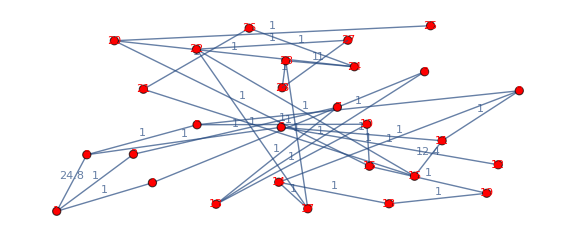

```mathematica
Graph[vl,edges,VertexCoordinates->{v_:>vd[[v, ;;2]]},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

```mathematica
GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}
```

GraphLayout→{SpringElectricalEmbedding,EdgeWeighted→True}

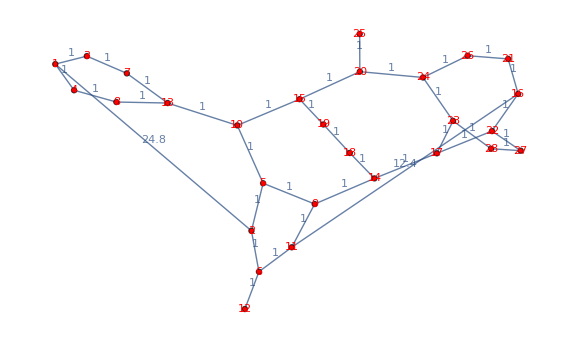

```mathematica
Graph[vl,edges,GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

```mathematica
Graph3D[vl,edges,GraphLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True},EdgeWeight->ew,VertexLabels->Placed["Name",Center],EdgeLabels->{e_:>Placed["EdgeWeight",.5]},VertexSize->.3,VertexStyle->Red,ImageSize->Large]
```

-Graphics3D-

```mathematica
vars=Array[Through[{x,y}@#]&,28]
```

{{x[1],y[1]},{x[2],y[2]},{x[3],y[3]},{x[4],y[4]},{x[5],y[5]},{x[6],y[6]},{x[7],y[7]},{x[8],y[8]},{x[9],y[9]},{x[10],y[10]},{x[11],y[11]},{x[12],y[12]},{x[13],y[13]},{x[14],y[14]},{x[15],y[15]},{x[16],y[16]},{x[17],y[17]},{x[18],y[18]},{x[19],y[19]},{x[20],y[20]},{x[21],y[21]},{x[22],y[22]},{x[23],y[23]},{x[24],y[24]},{x[25],y[25]},{x[26],y[26]},{x[27],y[27]},{x[28],y[28]}}

```mathematica
λ=1.;
obj=Total[(Norm[vars[[First@#]]-vars[[Last@#]]]-#/.ew)^2&/@EdgeList[g3d]]+λ Total[Norm/@(vars-vd[[All, ;;2]])];
```

```mathematica
solution=Last@Minimize[{obj,And@@Thread[0≤Join@@vars≤500]},Join@@vars];

edgeLengths=#->Norm[Through[{x,y}@First[#]]-Through[{x,y}@Last[#]]]/.solution&/@EdgeList[g3d];

Grid[Prepend[{#,#/.ew,#/.edgeLengths}&/@EdgeList[g3d],{"edge","EdgeWeight","Edge Length"}],Dividers->All]
```

Minimize::nmpt: Unable to find a point where the minimum is attained.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

1
 |  |  |  |

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Options::optnf: VertexCoordinates is not a known option for graph.